## Working with Quantum Circuits

```mathematica
<<Wolfram`QuantumFramework`
```

### Key Concepts

Circuit Depth

Pauli Matrices

### Specifying Circuits

You have already seen many examples using the Wolfram Quantum Framework. Let’s take a moment to explicitly learn more about the framework.

The framework supports a convenient shorthand notation for creating circuits. For example, consider the following circuit:

```mathematica
circuit1=QuantumCircuitOperator[{"0000","H"->1,"Z"->2}]
```

QuantumCircuitOperator[…]

This is shorthand for a 4-qubit input state, a Hadamard gate on the first qubit, and a Z gate on the second qubit. You can see the diagram using the "Diagram" property:

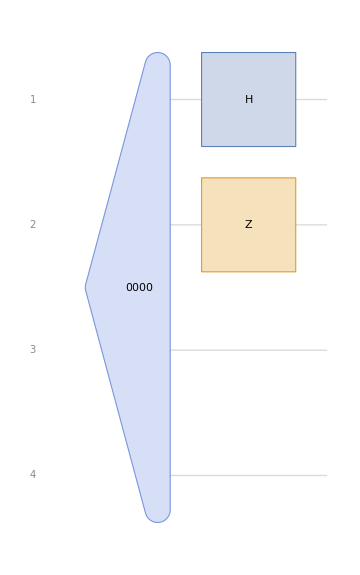

```mathematica
circuit1["Diagram"]
```

This circuit has no measurement operators. Thus, evaluating the circuit leads to a quantum state:

```mathematica
qs1=circuit1[]
```

QuantumState[…]

Every quantum state has a "Formula" property which shows the bra-ket (Dirac) notation:

```mathematica
qs1["Formula"]
```

1/(√2)0000+1/(√2)1000

You can build up larger quantum circuits by nesting QuantumCircuitOperator objects. The second argument can be used to label sub-circuits:

```mathematica
circuit2=QuantumCircuitOperator[{
QuantumCircuitOperator[circuit1,"First Part"],
QuantumCircuitOperator[{"SWAP"->{2,3},"CNOT"->{1,4}},"Second Part"],
"M"->Range[4]
}]
```

QuantumCircuitOperator[…]

This can be helpful if you want to label various parts of an algorithm’s diagram:

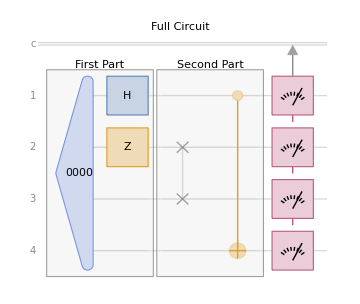

```mathematica
circuit2["Diagram",PlotLabel->"Full Circuit"]
```

This circuit now has measurements. Thus, evaluating it leads to a measurement object:

```mathematica
mea1=circuit2[]
```

QuantumMeasurement[…]

The measurement object can help you visualize the probability distribution or simply list the results:

```mathematica
mea1["Distribution"]
```

CategoricalDistribution[…]

```mathematica
mea1["Probability"]
```

<|0000→1/2,1001→1/2|>

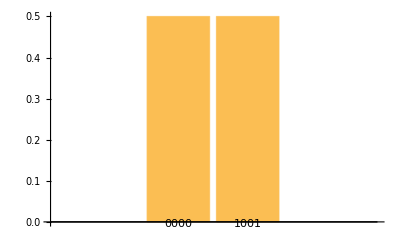

```mathematica
mea1["ProbabilityPlot"]
```

You can use this probability distribution to simulate measurement results if desired:

```mathematica
mea1["SimulatedMeasurement",1000]//Counts
```

<|0000→466,1001→534|>

### Equivalent Operators and Circuits

Given the measurement distribution in the last example, you might suspect that a simpler circuit could give equivalent results. This is usually the case when designing quantum algorithms. One of the key engineering challenges for practical quantum computing is creating circuits with few enough numbers of gates to run effectively.

Let’s look at another example.

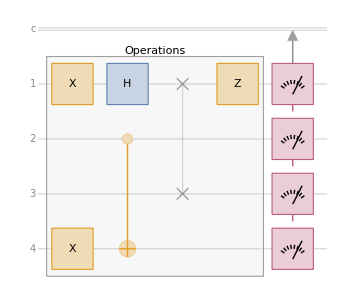

```mathematica
longops={"X"->1,"X"->4,"H"->1,"CNOT"->{2,4},"SWAP"->{1,3},"Z"->1};
longcircuit=QuantumCircuitOperator[{
QuantumCircuitOperator[longops,"Operations"],
"M"->Range[4]
}];
longcircuit["Diagram"]
```

The circuit depth is the maximum number of operations performed on any qubit.

```mathematica
longcircuit["Flatten"]["Depth"]
```

5

In this circuit, is it possible to come up with a different set of operations that lead to the same measurement results?

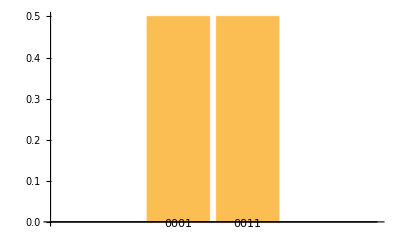

```mathematica
longcircuit[]["ProbabilityPlot"]
```

The simplicity of the measurement distribution certainly suggests this is the case. Consider the following circuit:

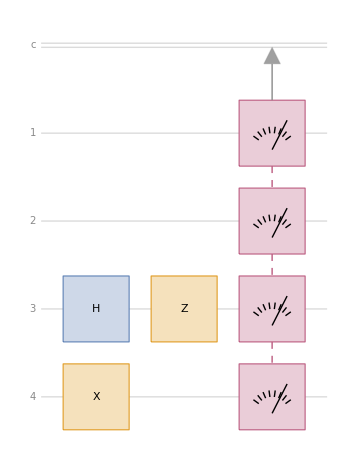

```mathematica
shortops={"H"->3,"Z"->3,"X"->4};
shortcircuit=QuantumCircuitOperator[{Splice@shortops,"M"->Range[4]}];
shortcircuit["Diagram"]
```

The circuit depth is shorter and the measurement distribution is identical:

```mathematica
shortcircuit["Depth"]
```

3

```mathematica
shortcircuit[]["ProbabilityPlot"]
```

-Graphics-

You can even verify that the quantum state after the long sequence of operations is the same as the quantum state after the short sequence of operations:

```mathematica
QuantumCircuitOperator[longops][]==QuantumCircuitOperator[shortops][]
```

True

Note that the states being equivalent before measurement is an even stronger requirement than just having identical measurement distributions.

### Pauli Operators

You might have noticed that an X gate seems to act a lot like a NOT gate. That’s because they have identical effects on qubits. An X gate is a NOT gate.

```mathematica
QuantumOperator["X"]==QuantumOperator["NOT"]
```

True

Recall the Bloch sphere representation of a qubit:

```mathematica
GraphicsGrid@Apply[
QuantumState[#2]["BlochPlot",PlotLabel->Highlighted[QuantumState[QuantumState[#2],#1],Background->LightOrange]]&,{{{"Z","Up"},{"Z","Down"}},{{"X","+"},{"X","-"}},{{"Y","R"},{"Y","L"}}},{2}]
```

-Graphics-

Each of the six states shown above lie along the Cartesian axes of the sphere. For various historical reasons, these states have alternate names in the context of quantum computing. However, they have another interpretation in the context of linear algebra. They simply correspond to eigenvectors of the Pauli matrices:

```mathematica
Table[PauliMatrix[k]//MatrixForm,{k,3}]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

```mathematica
Table[QuantumOperator[k]["Matrix"]//MatrixForm,{k,{"X","Y","Z"}}]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

A future lesson will discuss the matrix representation of quantum states in more detail.